# Tworzenie i optymalizacja filtrów FIR

## Raport 1 (25.03.2016)

Uniwersytet Jagielloński – Zakład Fotoniki

## Wstęp

Celem niniejszego raportu jest podsumowanie i przedstawienie wyników uzyskanych przy analizie filtrów typu FIR z myślą o zastosowaniu w układach FPGA (field-programmable gate array), jak również podkreślenie istotnych problemów napotkanych po drodze.

Zapis współczynników filtru w układach FPGA zazwyczaj ogranicza się do kilkunastu bitów na liczbę celem uzyskania możliwie największej wydajności, dlatego istotnym problemem staje się znalezienie ‘kompromisu’ pomiędzy liczbą współczynników oraz liczbą bitów (zwanej dalej dyskretyzacją) na których zostają zapisane.

Raport składa się z dwóch części: generowanie współczynników filtru oraz ich analizy.

### Właściwości transformaty Fouriera (przypomnienie)

Transformację Fouriera funkcji f(x) definiujemy jako F(s)=∫_(-∞)^∞ f(x)ⅇ^(-ⅈ 2π x s)ⅆx. Odwrotną zaś f(x)=∫_(-∞)^∞ F(s)ⅇ^(ⅈ 2π x s)ⅆs

Każdą funkcję możemy rozłożyć na część parzystą i nieparzystą, tj. f(x)=e(x)+o(x), gdzie: e(x)=1/2[f(x)+f(-x)], o(x)=1/2[f(x)-f(-x)].

Wtedy transformata Fouriera f(x) redukuje się do (całka iloczynu funkcji parzystej i nieparzystej jest nieparzysta):
∫_(-∞)^∞ e(x)cos(2π x s)ⅆx-ⅈ∫_(-∞)^∞ o(x)sin(2π x s)ⅆx

Widać stąd że transformata funkcji parzystej jest parzysta, a część rzeczywista pozostaje rzeczywista. Można też wyciągnąć więcej wniosków, które najlepiej podsumowuje poniższy rysunek:

-Graphics-

Diagram prezentujący transformatę funkcji 
(źródło ‘The Fourier Transform and it’s applications’ – Bracewell)

Zatem, aby operować (po wykonaniu transformaty) na wielkościach rzeczywistych, musimy ograniczyć się do parzystych funkcji.
W przypadku dyskretnej transformaty fouriera oś symetrii również przechodzi przez zero co prowadzi to do nieparzystej liczby próbek.
Konkretne implementacje różnią się od siebie, jednak często (również tutaj) do zapisu sygnału stosuje się tablice numerowane od 0, dlatego zwykle część próbek (normalnie znajdująca się po stronie ujemnych współczynników) dodawana jest na koniec tablicy.

## Znalezienie współczynników filtru

Współczynniki filtru FIR powinny zostać znalezione za pomocą kodu uruchamianego na CPU układu. Z tego powodu powstał program (filters.c) w języku C, wraz z programami pomocniczymi

(run-filters.c) mający na celu wygenerowanie współczynników filtru z zadanej, dyskretnej transmitancji w linii komend

(test-filters.c) generujący filtry lowpass/midpass i zapisujący je w plikach wraz z wieloma danymi pomocniczymi

Program używa istniejącej i otwartej biblioteki do transformaty fouriera zwanej KISS FTT (licencja BSD – http://kissfft.sourceforge.net).

Obecnie kod znajduje się w prywatnym repozytorium pod adresem: https://github.com/masteranza/SignalProcessing
oraz posiada szereg funkcji diagnostycznych ułatwiających szybkie testowanie filtrów, takie jak generacja filtrów low–, mid–pass.

### Kompilacja

Kompilacja run-filters.c oraz test-filters.c odbywa się za pomocą polecenia make.

make;

Opcjonalnie można skompilować pliki osobno za pomocą:

make runfilters;
make testfilters;

### Test w linii komend programu run-filters.c

Wygenerowanie filtru o transmitancji dyskretnej 1 1 1 0 0 używając 16 bitów:

./run-filters 16 1 1 1 0 0

### Format plików wyjściowych programu test-filters.c

Współczynniki generowane przez program są rzeczywiste, a ich ilość jest nieparzysta.
Zdyskretyzowane współczynniki również są rzeczywiste, dokładny opis procesu dyskretyzacji znajduje się w dalszej części.

Na obecną chwilę ilość danych w plikach wyjściowych jest również nadmiarowa.
Każdemu wierszowi odpowiada jeden współczynnik, jednak kolumn (dla potrzeb analizy i korekcji błędów) jest wiele, poniżej przedstawiono pełne zestawienie poszczególnych (numerowanych) kolumn.
Najistotniejszymi kolumnami są jednak kolumna: 1 (transmitancja), 9 (współczynniki) i 11 (zdyskretyzowane współczynniki)

1 – zadana na wejściu transmitancja używana przy obliczaniu współczynników, z możliwymi dodatkami, np. wygładzaniem stromych zboczy, domyślnie wyłączone
2 – część rzeczywista transmitancji obliczonej pomocniczo z obliczonych współczynników
3 – część urojona transmitancji obliczonej pomocniczo z obliczonych współczynników
4 – część rzeczywista transmitancji obliczonej pomocniczo z obliczonych, dyskretyzowanych współczynników
5 – część urojona transmitancji obliczonej pomocniczo z obliczonych, dyskretyzowanych współczynników
6 – wartość bezwględna współczynników (√(Re{wsp}^2+Im{wsp}^2))
7 – wartość bezwględna dyskretyzowanych współczynników
8 – numer współczynnika począwszy od 0.
9 – część rzeczywista współczynników
10 – część urojona współczynników (0)
11 – część rzeczywista zdyskretyzowanych współczynników
12 – część urojona zdyskretyzowanych współczynników (0)

### Przykład

Uruchomienie i wygenerowanie filtru low–pass o szerokości 10% (przepuszczającego 10% spektrum częstości) :

./test - filters 0.1

Uruchomienie i wygenerowanie filtru mid-pass o szerokości 10% i przesunięciem 30% (0% ≡ low–pass):

./test - filters 0.1 0.3

Efektem działania programu jest wygenerowanie szeregu plików (używanych później w dalszej analizie) o różnych długościach filtrów i różnej liczbie bitów użytych do dykretyzacji.

W przypadku filtrów low pass generowane są pliki postaci:

filtr⟨długość filtru⟩-⟨liczba bitów⟩.dat

gdzie ⟨długość filtru⟩ przybiera wartości: 31,63,127, 255, 511, 1023,
a ⟨liczba bitów⟩ wartości: 0, 2, 4,…,64.

Dla filtrów mid–pass sytuacja wygląda analogicznie, zmieniają się tylko nazwy plików, dla uniknięcia kolizji:

filtr⟨długość filtru⟩m-⟨liczba bitów⟩.dat

### Proces dyskretyzacji

Przy użyciu m bitów największą liczbą całkowitą możliwą do zapisania jest liczba 2^(m-1)-1 (pierwszy bit zarezerwowany jest do zapisu znaku).

Z tego powodu w procesie dyskretyzacji najpierw znajdywana jest największa (max) spośród liczb zapisanych w tablicy liczb x (i–ta liczba znajduje się pod x[i]). Następnie wszystkie liczby zostają podzielone/unormowane przez tę liczbę, a następnie przemnożone przez maksymalną liczbę (2^(m-1)-1) i zaokrąglone do najbliższej liczby całkowitej również ustalając jej znak. Aby z tak zdyskretyzowanej liczby uzyskać liczbę, odpowiadającą oryginalnej liczbie mnożymy przez czynnik odwrotny, a więc: max/(2^(m-1)-1).
Procedurę tę ilustruje pseudokod oraz znajdujący się poniżej przykład

```mathematica
xd[i]  = ((x[i] > 0) - (x[i] < 0))*round ((fabs (x[i])/max)*(pow (2, m - 1) - 1)) 
* max / (pow (2, m - 1) - 1);
```

m=4→2^(m-1)-1=7
a={1,-1,3,5} → max(a)=5 → a’={1/5, -1/5, 3/5, 1} → a’’={7/5, -7/5, 21/5, 7} → a’’’={1, -1, 4, 7}

Opisany wyżej proces dyskretyzacji, jest znacząco różny od zaokrąglenia liczb do najbliższej wielokrotności 2^-n. Przykład:
-Graphics-

## Analiza filtrów w programie Mathematica

W tej części przedstawiony zostaje końcowy zestaw skryptów użytych do analizy filtrów wraz z wynikami.

Aby skrypty mogły zostać ponownie przeliczone, należy najpierw dodać ścieżkę plików wyjściowych (znajdującą się katalog wyżej) do zmiennej $Path programu Mathematica

```mathematica
AppendTo[$Path,ParentDirectory[NotebookDirectory[]]];
```

### Inicjalizacja

```mathematica
(*stałe*)
nn={32,64,128,256,512,1024};
bits=Range[2,64,2];
(*Utworzenie macierzy nazw wygenerowanych przez test-filters plików*)
names=Outer["filtr"<>ToString[#1-1]<>"-"<>ToString[#2]<>".dat" &,nn,bits];
(*wykresy*)
leeg[xl_List,d_,points_List,numb_List,nam_List,args___]:=LogPlot[xl,d,
Epilog->{PointSize[Medium],Point[points],Inset[Panel[Grid[MapIndexed[{Graphics[{ColorData[1,First@#2],Thick,Line[{{0,0},{1,0}}]},AspectRatio->.1,ImageSize->20],First@nam[[#2]],First@numb[[#2]]}&,xl]]],Offset[{-2,2},Scaled[{1,1}]],{Right,Top}]},args];
TemperatureGrid[data_,bits_,args___]:=Grid[Prepend[Prepend[Map[Item[#,Background->ColorData[{"TemperatureMap",{Min[data],Max[data]}}][#]]&,data,{2}]ᵀ,nn]ᵀ,Prepend[bits,""]],args];
(*ustawienie WorkingDirectory*)
AppendTo[$Path,NotebookDirectory[]];
```

### Proste testy sprawdzające

#### Test w Mathematica

Interesującym testem który można przeprowadzić jest wyrysowanie wygenerowanych współczynników oraz porównanie transformaty tych współczynników wykonanej wewnątrz programu test-filters oraz w Mathematica. 
W tym celu na początek generujemy współczynniki filtrów szerokości 90% za pomocą polecenia:

```mathematica
./test-filters 0.9
```

lub bezpośrednio z notesu Mathematica:

```mathematica
szerokosc=0.9;
Run[OpenRead["!cd '"<>NotebookDirectory[]<>"'; ./test-filters "<>ToString[szerokosc]<>";"]];
```

Wczytujemy dane do notesu (należy zaczekać na wygenerowanie wszystkich plików):

```mathematica
(*wartość bezwględna transmitancji z programu test-filters*)
dataMag=Map[Import[#,"Data"][[All,7]]&,names,{2}];
(*zdyskretyzowane współczynniki filtru*)
dataWsp=Map[Import[#,"Data"][[All,11]]&,names,{2}];
```

Wybieramy dane dla przykładowej liczby współczynników: wsp=1 (2^(4+wsp)=32) oraz liczby bitów: bit=4 (bit*2=8) i wyświetlamy je:

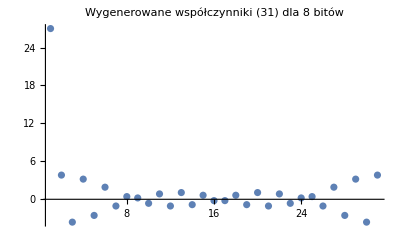

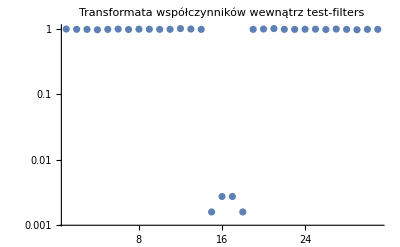
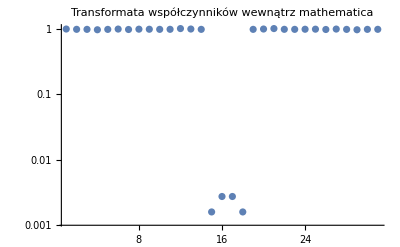

```mathematica
wsp=1;
bit=4;
ListPlot[dataWsp[[wsp,bit]],PlotRange->Full, PlotLabel->("Wygenerowane współczynniki ("<> ToString[2^(4+wsp)-1] <> ") dla " <> ToString[bit*2] <> " bitów")]
Row[{ListLogPlot[dataMag[[wsp,bit]]/(2^(4+wsp)-1),PlotRange->Full,PlotLabel->"Transformata współczynników\nwewnątrz test-filters"],
ListLogPlot[Abs@Fourier[dataWsp[[wsp,bit]], FourierParameters->{-1, 1}],PlotRange->Full,PlotLabel->"Transformata współczynników\nwewnątrz mathematica"]},BaseStyle->ImageSizeMultipliers->1]
```

Wyniki są identyczne z dokładnością do stałej (liczby współczynników).

### Szacowanie błędu

Przy szacowaniu błędu dyskretyzacji współczynników wypróbowano wiele miar, będących wariacjami średniego błędu kwadratowego (porównując transformaty współczynników), jednak bardzo dogodną miarą okazało się obliczenie średniego błędu względnego na jeden współczynnik z transmitancji T uzyskanego filtru.
Oznacza to, że przy porównywaniu filtrów, tak naprawdę porównujemy transmitancję (spektrum) filtru i filtru idealnego.

#### Średni błąd względny na jeden współczynnik

Oznaczmy spektrum filtru idealnego (wektor, składający się z N liczb) przez T, a przez T_M filtr (również składający się z N liczb) uzyskany przy zapisie na M bitach. Wtedy nasza miara wyraża się przez:

√((∑_(i=1)^N (T_M[i]-T[i])^2)/(∑_(i=1)^N (T[i])^2))

lub w przypadku ciągłym:

√((∫_0^π ⅆx (T_M[x]-T[x])^2)/(∫_0^π ⅆx (T[x])^2))

Aby możliwe było obliczenie błędu w przypadku ciągłym, należy wykonać najpierw DTFT (Discrete Time Fourier Transform) na zestawie uzyskanych współczynników.

## Wyniki

### Generowanie filtru low–pass i szacowanie błędu w procesie dyskretyzacji na M bitach

Poniższy kod pozwala na obliczenie błędów dyskretyzacji w zależności od ilości bitów i długości filtra o zadanej długości (domyślnie obliczenia przeprowadzane są na wygenerowanych wcześniej współczynnikach, jeśli jednak podamy na wejściu parametr “part” oznaczający szerokość fitru w % to współczynniki zostaną również dla nas wygenerowane)

```mathematica
CalcErrors[part_:0]:=Module[{transPlots,trans,transref,disc,dplots,start,names,data,rotData,data2,rotData2,dataPlot,dataPlot2,DTFT,rotDTFT,names2,dataDouble,data2Double,dataForInterLog,dataForInterDouble,interdDouble,idrotDTFTMeanSq,logDTFTs,listpoint,listpointd,dataPerfect,perfectDTFT,idDTFT},
If[part!=0,Run[OpenRead["!cd '"<>ParentDirectory[NotebookDirectory[]]<>"'; ./test-filters "<>ToString[part]<>";"]];Pause[10];];

names=Outer["filtr"<>ToString[#1-1]<>"-"<>ToString[#2]<>".dat" &,nn,bits];
data=Map[Import[#,"Data"][[All,11]]&,names,{2}];
trans=Map[Import[#,"Data"][[All,1]]&,names,{2}];
rotData=Map[RotateLeft[#,(Length@#+1)/2]&,data,{2}];

data2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,data,{2}];
rotData2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,rotData,{2}];

DTFT=Map[ListFourierSequenceTransform[#,x]/Length@(#)&,data,{2}];
rotDTFT=Map[ListFourierSequenceTransform[#,x]/Length@#&,rotData,{2}];
(*dataForInterLog= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,Log@#[[1;;(Length@#+1)/2]]}ᵀ &,data2,{2}];*)
names2=Outer["filtr"<>ToString[#1-1]<>"-64.dat" &,nn];
dataDouble=Map[Import[#,"Data"][[All,1]]&,names2];

dataPerfect=Map[Import[#,"Data"][[All,11]]&,names2,{1}];
perfectDTFT=Map[ListFourierSequenceTransform[#,x]/Length@(#)&,dataPerfect,{1}];

(*Średni błąd względny obliczony bezpośrednio na współczynnikach*)
(*Parallelize@Table[{part,len+4,Sqrt[Total[Abs[(data[[len,bit]]-dataPerfect[[len]])]^2]/((Total[Abs[dataPerfect[[len]]]^2] ) )]},{len,1,Length@DTFT}]*)
(*Średni Błąd względny(szerokosc, długość): miara dyskretna*)
Table[{bits[[bit]],len+4,Sqrt[Total[Abs[(data2[[len,bit]]-dataDouble[[len]])]^2]/((Total[Abs[dataDouble[[len]]]^2] ) )]},{len,1,Length@DTFT},{bit,1,Length@bits}]
(*Średni Błąd względny(szerokość, długość): miara ciągła*)
(*Table[{part,len+4,Sqrt[NIntegrate[Abs[DTFT[[len,bit]]-perfectDTFT[[len]]]^2,{x,0,π},AccuracyGoal->5,MaxRecursion->20]/NIntegrate[Abs[perfectDTFT[[len]]]^2,{x,0,π},AccuracyGoal->5,MaxRecursion->20]]},{len,1,Length@DTFT}]*)
(*Średni Błąd względny(bit, długość): miara dyskretna*)
(*Table[{2bit,len+4,Sqrt[Total[Abs[(data2[[len,bit]]-dataDouble[[len]])]^2]/((Total[Abs[dataDouble[[len]]]^2] ) )]},{len,1,Length@DTFT}]*)
];
```

### Zanik błędu z rosnącą liczbą bitów

Przechodzimy do obliczenia błędów dla filtru szerokości 0.25

```mathematica
wyniki=CalcErrors[0.25];
```

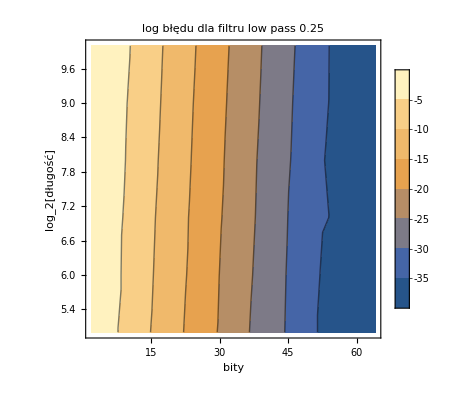

```mathematica
ListContourPlot[{#[[1]],#[[2]],Log[#[[3]]]}&/@Flatten[wyniki,1],PlotRange->Full,PlotLegends->Automatic,FrameLabel->{"bity","log_2[długość]"},PlotLabel->"log błędu dla filtru low pass 0.25"]
```

```mathematica
wyniki=CalcErrors[0.5];
```

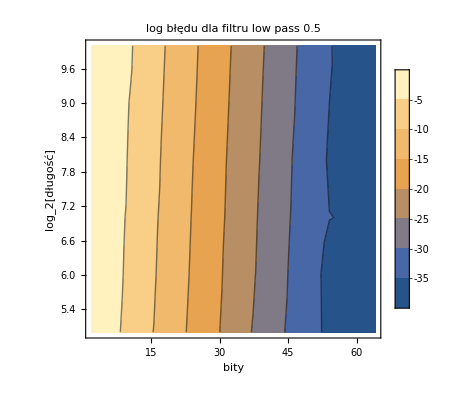

```mathematica
ListContourPlot[{#[[1]],#[[2]],Log[#[[3]]]}&/@Flatten[wyniki,1],PlotRange->Full,PlotLegends->Automatic,FrameLabel->{"bity","log_2[długość]"},PlotLabel->"log błędu dla filtru low pass 0.5"]
```

Dla zupełności rysujemy zależność błędu od szerokości filtru:

```mathematica
wynik=Table[CalcErrors[widt],{widt,0.1,0.9,0.1}];
```

```mathematica
ww2=Table[Flatten[Table[{#[[1]],i 0.1,Log@#[[3]]}&/@wynik[[All,j,All,All]][[i]],{i,1,Length@oneBit}],1],{j,1,Length@nn}];
```

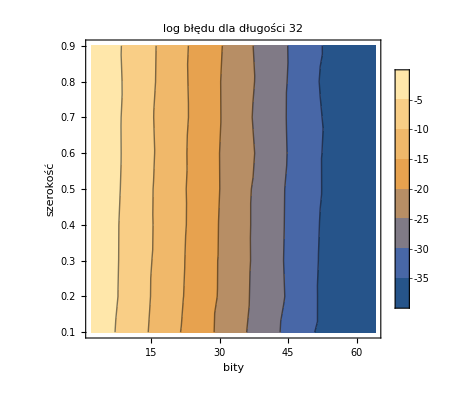
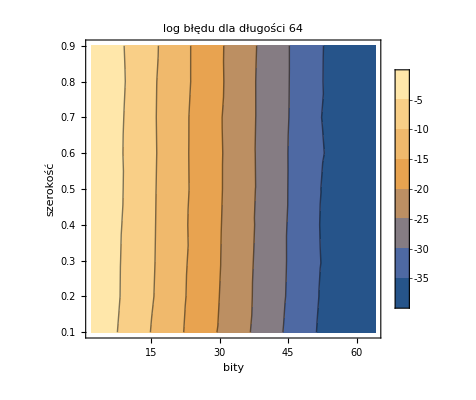
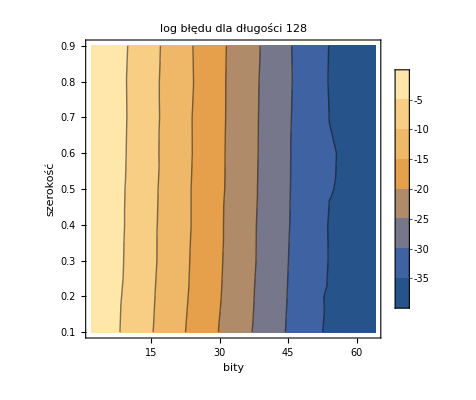
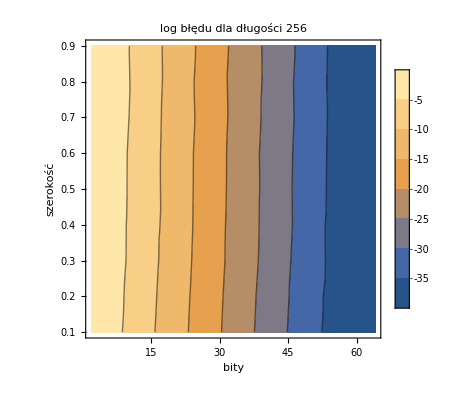
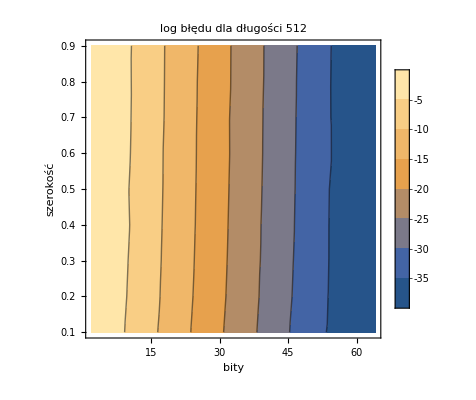
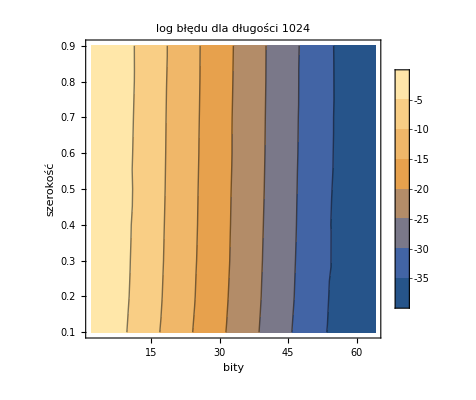
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Partition[Table[ListContourPlot[ww2[[j]],PlotLegends->Automatic,FrameLabel->{"bity","szerokość"},PlotLabel->"log błędu dla długości "<>ToString[nn[[j]]]<>""],{j,1,6}],3],BaseStyle->ImageSizeMultipliers->1]
```

Wykres wskazuje (na spodziewany) zanik błędu z rosnącą liczbę bitów oraz na drobny wzrost błędu w przypadku dłuższych filtrów.

Powyższy skrypt możemy wykorzystać również dla kilku szerokości filtrów, a następnie spojrzeć na interesujące nas ilości bitów:

```mathematica
wynik=Table[CalcErrors[widt],{widt,0.1,0.9,0.1}];
```

```mathematica
ww=Table[Flatten[Table[{i 0.1,#[[2]],#[[3]]}&/@wynik[[All,All,j,All]][[i]],{i,1,Length@oneBit}],1],{j,1,Length@bits}];
```

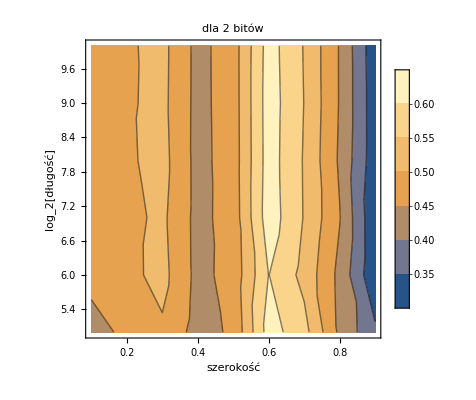
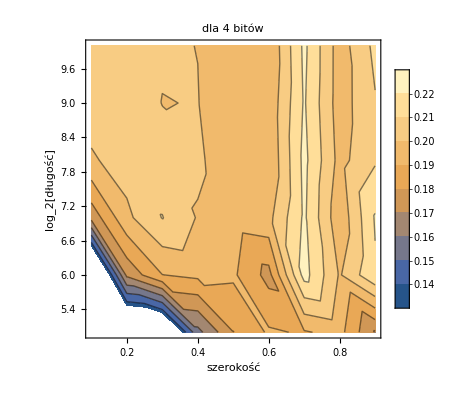
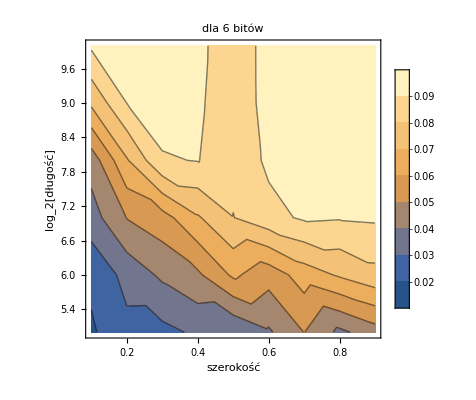
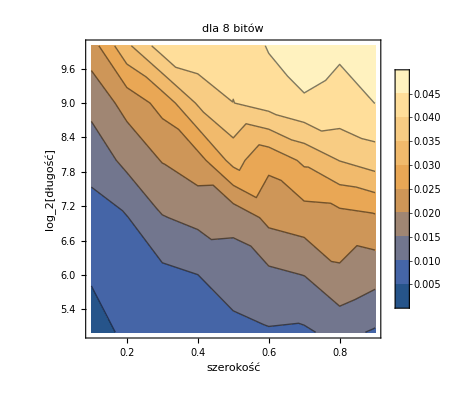
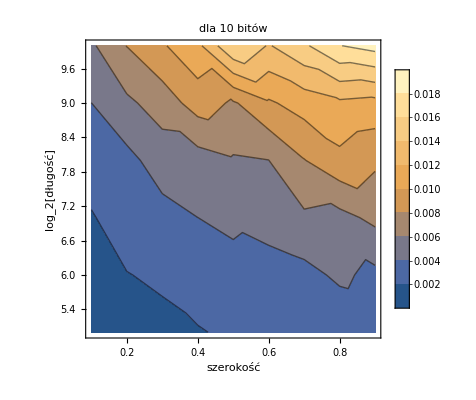
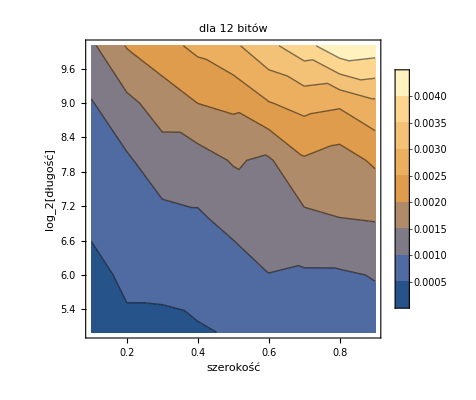
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Partition[Table[ListContourPlot[ww[[j]],PlotLegends->Automatic,FrameLabel->{"szerokość","log_2[długość]"},PlotLabel->"dla "<>ToString[bits[[j]]]<>" bitów"],{j,1,6}],3],BaseStyle->ImageSizeMultipliers->1]
```

### Problem rosnącego błędu z szerokością filtru

Nieco zastanawiający okazał się wzrost błędu przy rosnącej szerokości filtru, zwłaszcza (jak widać) w przypadku niskiej ilości bitów.
Do tej pory nie znaleziono zadowalającego wytłumaczenia tego fenomenu. 
Prosta heurystyka, przeprowadzona przy 6 bitach i mierze dyskretnej daje następujące wyniki dla filtrów 10% (pierwszy wiersz) i 90% (drugi wiersz):

-Graphics-

-Graphics-

Pierwsza kolumna przedstawia spektrum idealne i spektrum zdyskretyzowane na jednym wykresie, zaś druga przedstawia różnicę między nimi.
Licznik równania (Section.EquationNumbered) dla przypadku filtru 10% wynosi 0.00104495, a mianownik 3.
Dla filtru 90%, licznik wynosi 0.0555405, a mianownik 27.
Zatem błąd (liczony zgodnie z obraną miarą) zdecydowanie staje się większy gdy próbujemy utworzyć szerszy filtr.

## Podsumowanie

Przedstawiona tutaj metoda oraz zestaw skryptów pozwala na analizę jakości dowolnych filtrów z udziałem różnych miar – zarówno ciągłych jak i dyskretnych.
Dzięki uzyskanym wynikom można, w prosty sposób dopasować parametry pracy filtru FIR w zależności od możliwości dostępnego sprzętu.